## QM

### Create States

```mathematica
States=Flatten[Table[Table[{m,n},{n,m+1,L+2}],{m,1,L+2}],{1,2}]
```

{{1,2},{1,3},{1,4},{1,5},{1,6},{1,7},{1,8},{1,9},{1,10},{1,11},{1,12},{1,13},{1,14},{1,15},{1,16},{1,17},{1,18},{1,19},{1,20},{1,21},{1,22},{1,23},{1,24},{1,25},{1,26},{1,27},{1,28},{1,29},{1,30},{1,31},{1,32},{1,33},{1,34},{1,35},{1,36},{1,37},{1,38},{1,39},{1,40},{1,41},{1,42},{1,43},{1,44},{1,45},{1,46},{1,47},{1,48},{1,49},{1,50},{1,51},{1,52},{2,3},{2,4},{2,5},{2,6},{2,7},{2,8},{2,9},{2,10},{2,11},{2,12},{2,13},{2,14},{2,15},{2,16},{2,17},{2,18},{2,19},{2,20},{2,21},{2,22},{2,23},{2,24},{2,25},{2,26},{2,27},{2,28},{2,29},{2,30},{2,31},{2,32},{2,33},{2,34},{2,35},{2,36},{2,37},{2,38},{2,39},{2,40},{2,41},{2,42},{2,43},{2,44},{2,45},{2,46},{2,47},{2,48},{2,49},{2,50},{2,51},{2,52},{3,4},{3,5},{3,6},{3,7},{3,8},{3,9},{3,10},{3,11},{3,12},{3,13},{3,14},{3,15},{3,16},{3,17},{3,18},{3,19},{3,20},{3,21},{3,22},{3,23},{3,24},{3,25},{3,26},{3,27},{3,28},{3,29},{3,30},{3,31},{3,32},{3,33},{3,34},{3,35},{3,36},{3,37},{3,38},{3,39},{3,40},{3,41},{3,42},{3,43},{3,44},{3,45},{3,46},{3,47},{3,48},{3,49},{3,50},{3,51},{3,52},{4,5},{4,6},{4,7},{4,8},{4,9},{4,10},{4,11},{4,12},{4,13},{4,14},{4,15},{4,16},{4,17},{4,18},{4,19},{4,20},{4,21},{4,22},{4,23},{4,24},{4,25},{4,26},{4,27},{4,28},{4,29},{4,30},{4,31},{4,32},{4,33},{4,34},{4,35},{4,36},{4,37},{4,38},{4,39},{4,40},{4,41},{4,42},{4,43},{4,44},{4,45},{4,46},{4,47},{4,48},{4,49},{4,50},{4,51},{4,52},{5,6},{5,7},{5,8},{5,9},{5,10},{5,11},{5,12},{5,13},{5,14},{5,15},{5,16},{5,17},{5,18},{5,19},{5,20},{5,21},{5,22},{5,23},{5,24},{5,25},{5,26},{5,27},{5,28},{5,29},{5,30},{5,31},{5,32},{5,33},{5,34},{5,35},{5,36},{5,37},{5,38},{5,39},{5,40},{5,41},{5,42},{5,43},{5,44},{5,45},{5,46},{5,47},{5,48},{5,49},{5,50},{5,51},{5,52},{6,7},{6,8},{6,9},{6,10},{6,11},{6,12},{6,13},{6,14},{6,15},{6,16},{6,17},{6,18},{6,19},{6,20},{6,21},{6,22},{6,23},{6,24},{6,25},{6,26},{6,27},{6,28},{6,29},{6,30},{6,31},{6,32},{6,33},{6,34},{6,35},{6,36},{6,37},{6,38},{6,39},{6,40},{6,41},{6,42},{6,43},{6,44},{6,45},{6,46},{6,47},{6,48},{6,49},{6,50},{6,51},{6,52},{7,8},{7,9},{7,10},{7,11},{7,12},{7,13},{7,14},{7,15},{7,16},{7,17},{7,18},{7,19},{7,20},{7,21},{7,22},{7,23},{7,24},{7,25},{7,26},{7,27},{7,28},{7,29},{7,30},{7,31},{7,32},{7,33},{7,34},{7,35},{7,36},{7,37},{7,38},{7,39},{7,40},{7,41},{7,42},{7,43},{7,44},{7,45},{7,46},{7,47},{7,48},{7,49},{7,50},{7,51},{7,52},{8,9},{8,10},{8,11},{8,12},{8,13},{8,14},{8,15},{8,16},{8,17},{8,18},{8,19},{8,20},{8,21},{8,22},{8,23},{8,24},{8,25},{8,26},{8,27},{8,28},{8,29},{8,30},{8,31},{8,32},{8,33},{8,34},{8,35},{8,36},{8,37},{8,38},{8,39},{8,40},{8,41},{8,42},{8,43},{8,44},{8,45},{8,46},{8,47},{8,48},{8,49},{8,50},{8,51},{8,52},{9,10},{9,11},{9,12},{9,13},{9,14},{9,15},{9,16},{9,17},{9,18},{9,19},{9,20},{9,21},{9,22},{9,23},{9,24},{9,25},{9,26},{9,27},{9,28},{9,29},{9,30},{9,31},{9,32},{9,33},{9,34},{9,35},{9,36},{9,37},{9,38},{9,39},{9,40},{9,41},{9,42},{9,43},{9,44},{9,45},{9,46},{9,47},{9,48},{9,49},{9,50},{9,51},{9,52},{10,11},{10,12},{10,13},{10,14},{10,15},{10,16},{10,17},{10,18},{10,19},{10,20},{10,21},{10,22},{10,23},{10,24},{10,25},{10,26},{10,27},{10,28},{10,29},{10,30},{10,31},{10,32},{10,33},{10,34},{10,35},{10,36},{10,37},{10,38},{10,39},{10,40},{10,41},{10,42},{10,43},{10,44},{10,45},{10,46},{10,47},{10,48},{10,49},{10,50},{10,51},{10,52},{11,12},{11,13},{11,14},{11,15},{11,16},{11,17},{11,18},{11,19},{11,20},{11,21},{11,22},{11,23},{11,24},{11,25},{11,26},{11,27},{11,28},{11,29},{11,30},{11,31},{11,32},{11,33},{11,34},{11,35},{11,36},{11,37},{11,38},{11,39},{11,40},{11,41},{11,42},{11,43},{11,44},{11,45},{11,46},{11,47},{11,48},{11,49},{11,50},{11,51},{11,52},{12,13},{12,14},{12,15},{12,16},{12,17},{12,18},{12,19},{12,20},{12,21},{12,22},{12,23},{12,24},{12,25},{12,26},{12,27},{12,28},{12,29},{12,30},{12,31},{12,32},{12,33},{12,34},{12,35},{12,36},{12,37},{12,38},{12,39},{12,40},{12,41},{12,42},{12,43},{12,44},{12,45},{12,46},{12,47},{12,48},{12,49},{12,50},{12,51},{12,52},{13,14},{13,15},{13,16},{13,17},{13,18},{13,19},{13,20},{13,21},{13,22},{13,23},{13,24},{13,25},{13,26},{13,27},{13,28},{13,29},{13,30},{13,31},{13,32},{13,33},{13,34},{13,35},{13,36},{13,37},{13,38},{13,39},{13,40},{13,41},{13,42},{13,43},{13,44},{13,45},{13,46},{13,47},{13,48},{13,49},{13,50},{13,51},{13,52},{14,15},{14,16},{14,17},{14,18},{14,19},{14,20},{14,21},{14,22},{14,23},{14,24},{14,25},{14,26},{14,27},{14,28},{14,29},{14,30},{14,31},{14,32},{14,33},{14,34},{14,35},{14,36},{14,37},{14,38},{14,39},{14,40},{14,41},{14,42},{14,43},{14,44},{14,45},{14,46},{14,47},{14,48},{14,49},{14,50},{14,51},{14,52},{15,16},{15,17},{15,18},{15,19},{15,20},{15,21},{15,22},{15,23},{15,24},{15,25},{15,26},{15,27},{15,28},{15,29},{15,30},{15,31},{15,32},{15,33},{15,34},{15,35},{15,36},{15,37},{15,38},{15,39},{15,40},{15,41},{15,42},{15,43},{15,44},{15,45},{15,46},{15,47},{15,48},{15,49},{15,50},{15,51},{15,52},{16,17},{16,18},{16,19},{16,20},{16,21},{16,22},{16,23},{16,24},{16,25},{16,26},{16,27},{16,28},{16,29},{16,30},{16,31},{16,32},{16,33},{16,34},{16,35},{16,36},{16,37},{16,38},{16,39},{16,40},{16,41},{16,42},{16,43},{16,44},{16,45},{16,46},{16,47},{16,48},{16,49},{16,50},{16,51},{16,52},{17,18},{17,19},{17,20},{17,21},{17,22},{17,23},{17,24},{17,25},{17,26},{17,27},{17,28},{17,29},{17,30},{17,31},{17,32},{17,33},{17,34},{17,35},{17,36},{17,37},{17,38},{17,39},{17,40},{17,41},{17,42},{17,43},{17,44},{17,45},{17,46},{17,47},{17,48},{17,49},{17,50},{17,51},{17,52},{18,19},{18,20},{18,21},{18,22},{18,23},{18,24},{18,25},{18,26},{18,27},{18,28},{18,29},{18,30},{18,31},{18,32},{18,33},{18,34},{18,35},{18,36},{18,37},{18,38},{18,39},{18,40},{18,41},{18,42},{18,43},{18,44},{18,45},{18,46},{18,47},{18,48},{18,49},{18,50},{18,51},{18,52},{19,20},{19,21},{19,22},{19,23},{19,24},{19,25},{19,26},{19,27},{19,28},{19,29},{19,30},{19,31},{19,32},{19,33},{19,34},{19,35},{19,36},{19,37},{19,38},{19,39},{19,40},{19,41},{19,42},{19,43},{19,44},{19,45},{19,46},{19,47},{19,48},{19,49},{19,50},{19,51},{19,52},{20,21},{20,22},{20,23},{20,24},{20,25},{20,26},{20,27},{20,28},{20,29},{20,30},{20,31},{20,32},{20,33},{20,34},{20,35},{20,36},{20,37},{20,38},{20,39},{20,40},{20,41},{20,42},{20,43},{20,44},{20,45},{20,46},{20,47},{20,48},{20,49},{20,50},{20,51},{20,52},{21,22},{21,23},{21,24},{21,25},{21,26},{21,27},{21,28},{21,29},{21,30},{21,31},{21,32},{21,33},{21,34},{21,35},{21,36},{21,37},{21,38},{21,39},{21,40},{21,41},{21,42},{21,43},{21,44},{21,45},{21,46},{21,47},{21,48},{21,49},{21,50},{21,51},{21,52},{22,23},{22,24},{22,25},{22,26},{22,27},{22,28},{22,29},{22,30},{22,31},{22,32},{22,33},{22,34},{22,35},{22,36},{22,37},{22,38},{22,39},{22,40},{22,41},{22,42},{22,43},{22,44},{22,45},{22,46},{22,47},{22,48},{22,49},{22,50},{22,51},{22,52},{23,24},{23,25},{23,26},{23,27},{23,28},{23,29},{23,30},{23,31},{23,32},{23,33},{23,34},{23,35},{23,36},{23,37},{23,38},{23,39},{23,40},{23,41},{23,42},{23,43},{23,44},{23,45},{23,46},{23,47},{23,48},{23,49},{23,50},{23,51},{23,52},{24,25},{24,26},{24,27},{24,28},{24,29},{24,30},{24,31},{24,32},{24,33},{24,34},{24,35},{24,36},{24,37},{24,38},{24,39},{24,40},{24,41},{24,42},{24,43},{24,44},{24,45},{24,46},{24,47},{24,48},{24,49},{24,50},{24,51},{24,52},{25,26},{25,27},{25,28},{25,29},{25,30},{25,31},{25,32},{25,33},{25,34},{25,35},{25,36},{25,37},{25,38},{25,39},{25,40},{25,41},{25,42},{25,43},{25,44},{25,45},{25,46},{25,47},{25,48},{25,49},{25,50},{25,51},{25,52},{26,27},{26,28},{26,29},{26,30},{26,31},{26,32},{26,33},{26,34},{26,35},{26,36},{26,37},{26,38},{26,39},{26,40},{26,41},{26,42},{26,43},{26,44},{26,45},{26,46},{26,47},{26,48},{26,49},{26,50},{26,51},{26,52},{27,28},{27,29},{27,30},{27,31},{27,32},{27,33},{27,34},{27,35},{27,36},{27,37},{27,38},{27,39},{27,40},{27,41},{27,42},{27,43},{27,44},{27,45},{27,46},{27,47},{27,48},{27,49},{27,50},{27,51},{27,52},{28,29},{28,30},{28,31},{28,32},{28,33},{28,34},{28,35},{28,36},{28,37},{28,38},{28,39},{28,40},{28,41},{28,42},{28,43},{28,44},{28,45},{28,46},{28,47},{28,48},{28,49},{28,50},{28,51},{28,52},{29,30},{29,31},{29,32},{29,33},{29,34},{29,35},{29,36},{29,37},{29,38},{29,39},{29,40},{29,41},{29,42},{29,43},{29,44},{29,45},{29,46},{29,47},{29,48},{29,49},{29,50},{29,51},{29,52},{30,31},{30,32},{30,33},{30,34},{30,35},{30,36},{30,37},{30,38},{30,39},{30,40},{30,41},{30,42},{30,43},{30,44},{30,45},{30,46},{30,47},{30,48},{30,49},{30,50},{30,51},{30,52},{31,32},{31,33},{31,34},{31,35},{31,36},{31,37},{31,38},{31,39},{31,40},{31,41},{31,42},{31,43},{31,44},{31,45},{31,46},{31,47},{31,48},{31,49},{31,50},{31,51},{31,52},{32,33},{32,34},{32,35},{32,36},{32,37},{32,38},{32,39},{32,40},{32,41},{32,42},{32,43},{32,44},{32,45},{32,46},{32,47},{32,48},{32,49},{32,50},{32,51},{32,52},{33,34},{33,35},{33,36},{33,37},{33,38},{33,39},{33,40},{33,41},{33,42},{33,43},{33,44},{33,45},{33,46},{33,47},{33,48},{33,49},{33,50},{33,51},{33,52},{34,35},{34,36},{34,37},{34,38},{34,39},{34,40},{34,41},{34,42},{34,43},{34,44},{34,45},{34,46},{34,47},{34,48},{34,49},{34,50},{34,51},{34,52},{35,36},{35,37},{35,38},{35,39},{35,40},{35,41},{35,42},{35,43},{35,44},{35,45},{35,46},{35,47},{35,48},{35,49},{35,50},{35,51},{35,52},{36,37},{36,38},{36,39},{36,40},{36,41},{36,42},{36,43},{36,44},{36,45},{36,46},{36,47},{36,48},{36,49},{36,50},{36,51},{36,52},{37,38},{37,39},{37,40},{37,41},{37,42},{37,43},{37,44},{37,45},{37,46},{37,47},{37,48},{37,49},{37,50},{37,51},{37,52},{38,39},{38,40},{38,41},{38,42},{38,43},{38,44},{38,45},{38,46},{38,47},{38,48},{38,49},{38,50},{38,51},{38,52},{39,40},{39,41},{39,42},{39,43},{39,44},{39,45},{39,46},{39,47},{39,48},{39,49},{39,50},{39,51},{39,52},{40,41},{40,42},{40,43},{40,44},{40,45},{40,46},{40,47},{40,48},{40,49},{40,50},{40,51},{40,52},{41,42},{41,43},{41,44},{41,45},{41,46},{41,47},{41,48},{41,49},{41,50},{41,51},{41,52},{42,43},{42,44},{42,45},{42,46},{42,47},{42,48},{42,49},{42,50},{42,51},{42,52},{43,44},{43,45},{43,46},{43,47},{43,48},{43,49},{43,50},{43,51},{43,52},{44,45},{44,46},{44,47},{44,48},{44,49},{44,50},{44,51},{44,52},{45,46},{45,47},{45,48},{45,49},{45,50},{45,51},{45,52},{46,47},{46,48},{46,49},{46,50},{46,51},{46,52},{47,48},{47,49},{47,50},{47,51},{47,52},{48,49},{48,50},{48,51},{48,52},{49,50},{49,51},{49,52},{50,51},{50,52},{51,52}}

```mathematica
Num[{a_,b_}]:=(a-1)/2(2L+4-a)+b-a;
```

```mathematica
Table[Num[States[[n]]],{n,1,M}]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100,101,102,103,104,105,106,107,108,109,110,111,112,113,114,115,116,117,118,119,120,121,122,123,124,125,126,127,128,129,130,131,132,133,134,135,136,137,138,139,140,141,142,143,144,145,146,147,148,149,150,151,152,153,154,155,156,157,158,159,160,161,162,163,164,165,166,167,168,169,170,171,172,173,174,175,176,177,178,179,180,181,182,183,184,185,186,187,188,189,190,191,192,193,194,195,196,197,198,199,200,201,202,203,204,205,206,207,208,209,210,211,212,213,214,215,216,217,218,219,220,221,222,223,224,225,226,227,228,229,230,231,232,233,234,235,236,237,238,239,240,241,242,243,244,245,246,247,248,249,250,251,252,253,254,255,256,257,258,259,260,261,262,263,264,265,266,267,268,269,270,271,272,273,274,275,276,277,278,279,280,281,282,283,284,285,286,287,288,289,290,291,292,293,294,295,296,297,298,299,300,301,302,303,304,305,306,307,308,309,310,311,312,313,314,315,316,317,318,319,320,321,322,323,324,325,326,327,328,329,330,331,332,333,334,335,336,337,338,339,340,341,342,343,344,345,346,347,348,349,350,351,352,353,354,355,356,357,358,359,360,361,362,363,364,365,366,367,368,369,370,371,372,373,374,375,376,377,378,379,380,381,382,383,384,385,386,387,388,389,390,391,392,393,394,395,396,397,398,399,400,401,402,403,404,405,406,407,408,409,410,411,412,413,414,415,416,417,418,419,420,421,422,423,424,425,426,427,428,429,430,431,432,433,434,435,436,437,438,439,440,441,442,443,444,445,446,447,448,449,450,451,452,453,454,455,456,457,458,459,460,461,462,463,464,465,466,467,468,469,470,471,472,473,474,475,476,477,478,479,480,481,482,483,484,485,486,487,488,489,490,491,492,493,494,495,496,497,498,499,500,501,502,503,504,505,506,507,508,509,510,511,512,513,514,515,516,517,518,519,520,521,522,523,524,525,526,527,528,529,530,531,532,533,534,535,536,537,538,539,540,541,542,543,544,545,546,547,548,549,550,551,552,553,554,555,556,557,558,559,560,561,562,563,564,565,566,567,568,569,570,571,572,573,574,575,576,577,578,579,580,581,582,583,584,585,586,587,588,589,590,591,592,593,594,595,596,597,598,599,600,601,602,603,604,605,606,607,608,609,610,611,612,613,614,615,616,617,618,619,620,621,622,623,624,625,626,627,628,629,630,631,632,633,634,635,636,637,638,639,640,641,642,643,644,645,646,647,648,649,650,651,652,653,654,655,656,657,658,659,660,661,662,663,664,665,666,667,668,669,670,671,672,673,674,675,676,677,678,679,680,681,682,683,684,685,686,687,688,689,690,691,692,693,694,695,696,697,698,699,700,701,702,703,704,705,706,707,708,709,710,711,712,713,714,715,716,717,718,719,720,721,722,723,724,725,726,727,728,729,730,731,732,733,734,735,736,737,738,739,740,741,742,743,744,745,746,747,748,749,750,751,752,753,754,755,756,757,758,759,760,761,762,763,764,765,766,767,768,769,770,771,772,773,774,775,776,777,778,779,780,781,782,783,784,785,786,787,788,789,790,791,792,793,794,795,796,797,798,799,800,801,802,803,804,805,806,807,808,809,810,811,812,813,814,815,816,817,818,819,820,821,822,823,824,825,826,827,828,829,830,831,832,833,834,835,836,837,838,839,840,841,842,843,844,845,846,847,848,849,850,851,852,853,854,855,856,857,858,859,860,861,862,863,864,865,866,867,868,869,870,871,872,873,874,875,876,877,878,879,880,881,882,883,884,885,886,887,888,889,890,891,892,893,894,895,896,897,898,899,900,901,902,903,904,905,906,907,908,909,910,911,912,913,914,915,916,917,918,919,920,921,922,923,924,925,926,927,928,929,930,931,932,933,934,935,936,937,938,939,940,941,942,943,944,945,946,947,948,949,950,951,952,953,954,955,956,957,958,959,960,961,962,963,964,965,966,967,968,969,970,971,972,973,974,975,976,977,978,979,980,981,982,983,984,985,986,987,988,989,990,991,992,993,994,995,996,997,998,999,1000,1001,1002,1003,1004,1005,1006,1007,1008,1009,1010,1011,1012,1013,1014,1015,1016,1017,1018,1019,1020,1021,1022,1023,1024,1025,1026,1027,1028,1029,1030,1031,1032,1033,1034,1035,1036,1037,1038,1039,1040,1041,1042,1043,1044,1045,1046,1047,1048,1049,1050,1051,1052,1053,1054,1055,1056,1057,1058,1059,1060,1061,1062,1063,1064,1065,1066,1067,1068,1069,1070,1071,1072,1073,1074,1075,1076,1077,1078,1079,1080,1081,1082,1083,1084,1085,1086,1087,1088,1089,1090,1091,1092,1093,1094,1095,1096,1097,1098,1099,1100,1101,1102,1103,1104,1105,1106,1107,1108,1109,1110,1111,1112,1113,1114,1115,1116,1117,1118,1119,1120,1121,1122,1123,1124,1125,1126,1127,1128,1129,1130,1131,1132,1133,1134,1135,1136,1137,1138,1139,1140,1141,1142,1143,1144,1145,1146,1147,1148,1149,1150,1151,1152,1153,1154,1155,1156,1157,1158,1159,1160,1161,1162,1163,1164,1165,1166,1167,1168,1169,1170,1171,1172,1173,1174,1175,1176,1177,1178,1179,1180,1181,1182,1183,1184,1185,1186,1187,1188,1189,1190,1191,1192,1193,1194,1195,1196,1197,1198,1199,1200,1201,1202,1203,1204,1205,1206,1207,1208,1209,1210,1211,1212,1213,1214,1215,1216,1217,1218,1219,1220,1221,1222,1223,1224,1225,1226,1227,1228,1229,1230,1231,1232,1233,1234,1235,1236,1237,1238,1239,1240,1241,1242,1243,1244,1245,1246,1247,1248,1249,1250,1251,1252,1253,1254,1255,1256,1257,1258,1259,1260,1261,1262,1263,1264,1265,1266,1267,1268,1269,1270,1271,1272,1273,1274,1275,1276,1277,1278,1279,1280,1281,1282,1283,1284,1285,1286,1287,1288,1289,1290,1291,1292,1293,1294,1295,1296,1297,1298,1299,1300,1301,1302,1303,1304,1305,1306,1307,1308,1309,1310,1311,1312,1313,1314,1315,1316,1317,1318,1319,1320,1321,1322,1323,1324,1325,1326}

```mathematica
OtherRep={States[[All,1]]-1,States[[All,2]]-States[[All,1]]-1,L+2-States[[All,2]]}ᵀ
```

{{0,0,50},{0,1,49},{0,2,48},{0,3,47},{0,4,46},{0,5,45},{0,6,44},{0,7,43},{0,8,42},{0,9,41},{0,10,40},{0,11,39},{0,12,38},{0,13,37},{0,14,36},{0,15,35},{0,16,34},{0,17,33},{0,18,32},{0,19,31},{0,20,30},{0,21,29},{0,22,28},{0,23,27},{0,24,26},{0,25,25},{0,26,24},{0,27,23},{0,28,22},{0,29,21},{0,30,20},{0,31,19},{0,32,18},{0,33,17},{0,34,16},{0,35,15},{0,36,14},{0,37,13},{0,38,12},{0,39,11},{0,40,10},{0,41,9},{0,42,8},{0,43,7},{0,44,6},{0,45,5},{0,46,4},{0,47,3},{0,48,2},{0,49,1},{0,50,0},{1,0,49},{1,1,48},{1,2,47},{1,3,46},{1,4,45},{1,5,44},{1,6,43},{1,7,42},{1,8,41},{1,9,40},{1,10,39},{1,11,38},{1,12,37},{1,13,36},{1,14,35},{1,15,34},{1,16,33},{1,17,32},{1,18,31},{1,19,30},{1,20,29},{1,21,28},{1,22,27},{1,23,26},{1,24,25},{1,25,24},{1,26,23},{1,27,22},{1,28,21},{1,29,20},{1,30,19},{1,31,18},{1,32,17},{1,33,16},{1,34,15},{1,35,14},{1,36,13},{1,37,12},{1,38,11},{1,39,10},{1,40,9},{1,41,8},{1,42,7},{1,43,6},{1,44,5},{1,45,4},{1,46,3},{1,47,2},{1,48,1},{1,49,0},{2,0,48},{2,1,47},{2,2,46},{2,3,45},{2,4,44},{2,5,43},{2,6,42},{2,7,41},{2,8,40},{2,9,39},{2,10,38},{2,11,37},{2,12,36},{2,13,35},{2,14,34},{2,15,33},{2,16,32},{2,17,31},{2,18,30},{2,19,29},{2,20,28},{2,21,27},{2,22,26},{2,23,25},{2,24,24},{2,25,23},{2,26,22},{2,27,21},{2,28,20},{2,29,19},{2,30,18},{2,31,17},{2,32,16},{2,33,15},{2,34,14},{2,35,13},{2,36,12},{2,37,11},{2,38,10},{2,39,9},{2,40,8},{2,41,7},{2,42,6},{2,43,5},{2,44,4},{2,45,3},{2,46,2},{2,47,1},{2,48,0},{3,0,47},{3,1,46},{3,2,45},{3,3,44},{3,4,43},{3,5,42},{3,6,41},{3,7,40},{3,8,39},{3,9,38},{3,10,37},{3,11,36},{3,12,35},{3,13,34},{3,14,33},{3,15,32},{3,16,31},{3,17,30},{3,18,29},{3,19,28},{3,20,27},{3,21,26},{3,22,25},{3,23,24},{3,24,23},{3,25,22},{3,26,21},{3,27,20},{3,28,19},{3,29,18},{3,30,17},{3,31,16},{3,32,15},{3,33,14},{3,34,13},{3,35,12},{3,36,11},{3,37,10},{3,38,9},{3,39,8},{3,40,7},{3,41,6},{3,42,5},{3,43,4},{3,44,3},{3,45,2},{3,46,1},{3,47,0},{4,0,46},{4,1,45},{4,2,44},{4,3,43},{4,4,42},{4,5,41},{4,6,40},{4,7,39},{4,8,38},{4,9,37},{4,10,36},{4,11,35},{4,12,34},{4,13,33},{4,14,32},{4,15,31},{4,16,30},{4,17,29},{4,18,28},{4,19,27},{4,20,26},{4,21,25},{4,22,24},{4,23,23},{4,24,22},{4,25,21},{4,26,20},{4,27,19},{4,28,18},{4,29,17},{4,30,16},{4,31,15},{4,32,14},{4,33,13},{4,34,12},{4,35,11},{4,36,10},{4,37,9},{4,38,8},{4,39,7},{4,40,6},{4,41,5},{4,42,4},{4,43,3},{4,44,2},{4,45,1},{4,46,0},{5,0,45},{5,1,44},{5,2,43},{5,3,42},{5,4,41},{5,5,40},{5,6,39},{5,7,38},{5,8,37},{5,9,36},{5,10,35},{5,11,34},{5,12,33},{5,13,32},{5,14,31},{5,15,30},{5,16,29},{5,17,28},{5,18,27},{5,19,26},{5,20,25},{5,21,24},{5,22,23},{5,23,22},{5,24,21},{5,25,20},{5,26,19},{5,27,18},{5,28,17},{5,29,16},{5,30,15},{5,31,14},{5,32,13},{5,33,12},{5,34,11},{5,35,10},{5,36,9},{5,37,8},{5,38,7},{5,39,6},{5,40,5},{5,41,4},{5,42,3},{5,43,2},{5,44,1},{5,45,0},{6,0,44},{6,1,43},{6,2,42},{6,3,41},{6,4,40},{6,5,39},{6,6,38},{6,7,37},{6,8,36},{6,9,35},{6,10,34},{6,11,33},{6,12,32},{6,13,31},{6,14,30},{6,15,29},{6,16,28},{6,17,27},{6,18,26},{6,19,25},{6,20,24},{6,21,23},{6,22,22},{6,23,21},{6,24,20},{6,25,19},{6,26,18},{6,27,17},{6,28,16},{6,29,15},{6,30,14},{6,31,13},{6,32,12},{6,33,11},{6,34,10},{6,35,9},{6,36,8},{6,37,7},{6,38,6},{6,39,5},{6,40,4},{6,41,3},{6,42,2},{6,43,1},{6,44,0},{7,0,43},{7,1,42},{7,2,41},{7,3,40},{7,4,39},{7,5,38},{7,6,37},{7,7,36},{7,8,35},{7,9,34},{7,10,33},{7,11,32},{7,12,31},{7,13,30},{7,14,29},{7,15,28},{7,16,27},{7,17,26},{7,18,25},{7,19,24},{7,20,23},{7,21,22},{7,22,21},{7,23,20},{7,24,19},{7,25,18},{7,26,17},{7,27,16},{7,28,15},{7,29,14},{7,30,13},{7,31,12},{7,32,11},{7,33,10},{7,34,9},{7,35,8},{7,36,7},{7,37,6},{7,38,5},{7,39,4},{7,40,3},{7,41,2},{7,42,1},{7,43,0},{8,0,42},{8,1,41},{8,2,40},{8,3,39},{8,4,38},{8,5,37},{8,6,36},{8,7,35},{8,8,34},{8,9,33},{8,10,32},{8,11,31},{8,12,30},{8,13,29},{8,14,28},{8,15,27},{8,16,26},{8,17,25},{8,18,24},{8,19,23},{8,20,22},{8,21,21},{8,22,20},{8,23,19},{8,24,18},{8,25,17},{8,26,16},{8,27,15},{8,28,14},{8,29,13},{8,30,12},{8,31,11},{8,32,10},{8,33,9},{8,34,8},{8,35,7},{8,36,6},{8,37,5},{8,38,4},{8,39,3},{8,40,2},{8,41,1},{8,42,0},{9,0,41},{9,1,40},{9,2,39},{9,3,38},{9,4,37},{9,5,36},{9,6,35},{9,7,34},{9,8,33},{9,9,32},{9,10,31},{9,11,30},{9,12,29},{9,13,28},{9,14,27},{9,15,26},{9,16,25},{9,17,24},{9,18,23},{9,19,22},{9,20,21},{9,21,20},{9,22,19},{9,23,18},{9,24,17},{9,25,16},{9,26,15},{9,27,14},{9,28,13},{9,29,12},{9,30,11},{9,31,10},{9,32,9},{9,33,8},{9,34,7},{9,35,6},{9,36,5},{9,37,4},{9,38,3},{9,39,2},{9,40,1},{9,41,0},{10,0,40},{10,1,39},{10,2,38},{10,3,37},{10,4,36},{10,5,35},{10,6,34},{10,7,33},{10,8,32},{10,9,31},{10,10,30},{10,11,29},{10,12,28},{10,13,27},{10,14,26},{10,15,25},{10,16,24},{10,17,23},{10,18,22},{10,19,21},{10,20,20},{10,21,19},{10,22,18},{10,23,17},{10,24,16},{10,25,15},{10,26,14},{10,27,13},{10,28,12},{10,29,11},{10,30,10},{10,31,9},{10,32,8},{10,33,7},{10,34,6},{10,35,5},{10,36,4},{10,37,3},{10,38,2},{10,39,1},{10,40,0},{11,0,39},{11,1,38},{11,2,37},{11,3,36},{11,4,35},{11,5,34},{11,6,33},{11,7,32},{11,8,31},{11,9,30},{11,10,29},{11,11,28},{11,12,27},{11,13,26},{11,14,25},{11,15,24},{11,16,23},{11,17,22},{11,18,21},{11,19,20},{11,20,19},{11,21,18},{11,22,17},{11,23,16},{11,24,15},{11,25,14},{11,26,13},{11,27,12},{11,28,11},{11,29,10},{11,30,9},{11,31,8},{11,32,7},{11,33,6},{11,34,5},{11,35,4},{11,36,3},{11,37,2},{11,38,1},{11,39,0},{12,0,38},{12,1,37},{12,2,36},{12,3,35},{12,4,34},{12,5,33},{12,6,32},{12,7,31},{12,8,30},{12,9,29},{12,10,28},{12,11,27},{12,12,26},{12,13,25},{12,14,24},{12,15,23},{12,16,22},{12,17,21},{12,18,20},{12,19,19},{12,20,18},{12,21,17},{12,22,16},{12,23,15},{12,24,14},{12,25,13},{12,26,12},{12,27,11},{12,28,10},{12,29,9},{12,30,8},{12,31,7},{12,32,6},{12,33,5},{12,34,4},{12,35,3},{12,36,2},{12,37,1},{12,38,0},{13,0,37},{13,1,36},{13,2,35},{13,3,34},{13,4,33},{13,5,32},{13,6,31},{13,7,30},{13,8,29},{13,9,28},{13,10,27},{13,11,26},{13,12,25},{13,13,24},{13,14,23},{13,15,22},{13,16,21},{13,17,20},{13,18,19},{13,19,18},{13,20,17},{13,21,16},{13,22,15},{13,23,14},{13,24,13},{13,25,12},{13,26,11},{13,27,10},{13,28,9},{13,29,8},{13,30,7},{13,31,6},{13,32,5},{13,33,4},{13,34,3},{13,35,2},{13,36,1},{13,37,0},{14,0,36},{14,1,35},{14,2,34},{14,3,33},{14,4,32},{14,5,31},{14,6,30},{14,7,29},{14,8,28},{14,9,27},{14,10,26},{14,11,25},{14,12,24},{14,13,23},{14,14,22},{14,15,21},{14,16,20},{14,17,19},{14,18,18},{14,19,17},{14,20,16},{14,21,15},{14,22,14},{14,23,13},{14,24,12},{14,25,11},{14,26,10},{14,27,9},{14,28,8},{14,29,7},{14,30,6},{14,31,5},{14,32,4},{14,33,3},{14,34,2},{14,35,1},{14,36,0},{15,0,35},{15,1,34},{15,2,33},{15,3,32},{15,4,31},{15,5,30},{15,6,29},{15,7,28},{15,8,27},{15,9,26},{15,10,25},{15,11,24},{15,12,23},{15,13,22},{15,14,21},{15,15,20},{15,16,19},{15,17,18},{15,18,17},{15,19,16},{15,20,15},{15,21,14},{15,22,13},{15,23,12},{15,24,11},{15,25,10},{15,26,9},{15,27,8},{15,28,7},{15,29,6},{15,30,5},{15,31,4},{15,32,3},{15,33,2},{15,34,1},{15,35,0},{16,0,34},{16,1,33},{16,2,32},{16,3,31},{16,4,30},{16,5,29},{16,6,28},{16,7,27},{16,8,26},{16,9,25},{16,10,24},{16,11,23},{16,12,22},{16,13,21},{16,14,20},{16,15,19},{16,16,18},{16,17,17},{16,18,16},{16,19,15},{16,20,14},{16,21,13},{16,22,12},{16,23,11},{16,24,10},{16,25,9},{16,26,8},{16,27,7},{16,28,6},{16,29,5},{16,30,4},{16,31,3},{16,32,2},{16,33,1},{16,34,0},{17,0,33},{17,1,32},{17,2,31},{17,3,30},{17,4,29},{17,5,28},{17,6,27},{17,7,26},{17,8,25},{17,9,24},{17,10,23},{17,11,22},{17,12,21},{17,13,20},{17,14,19},{17,15,18},{17,16,17},{17,17,16},{17,18,15},{17,19,14},{17,20,13},{17,21,12},{17,22,11},{17,23,10},{17,24,9},{17,25,8},{17,26,7},{17,27,6},{17,28,5},{17,29,4},{17,30,3},{17,31,2},{17,32,1},{17,33,0},{18,0,32},{18,1,31},{18,2,30},{18,3,29},{18,4,28},{18,5,27},{18,6,26},{18,7,25},{18,8,24},{18,9,23},{18,10,22},{18,11,21},{18,12,20},{18,13,19},{18,14,18},{18,15,17},{18,16,16},{18,17,15},{18,18,14},{18,19,13},{18,20,12},{18,21,11},{18,22,10},{18,23,9},{18,24,8},{18,25,7},{18,26,6},{18,27,5},{18,28,4},{18,29,3},{18,30,2},{18,31,1},{18,32,0},{19,0,31},{19,1,30},{19,2,29},{19,3,28},{19,4,27},{19,5,26},{19,6,25},{19,7,24},{19,8,23},{19,9,22},{19,10,21},{19,11,20},{19,12,19},{19,13,18},{19,14,17},{19,15,16},{19,16,15},{19,17,14},{19,18,13},{19,19,12},{19,20,11},{19,21,10},{19,22,9},{19,23,8},{19,24,7},{19,25,6},{19,26,5},{19,27,4},{19,28,3},{19,29,2},{19,30,1},{19,31,0},{20,0,30},{20,1,29},{20,2,28},{20,3,27},{20,4,26},{20,5,25},{20,6,24},{20,7,23},{20,8,22},{20,9,21},{20,10,20},{20,11,19},{20,12,18},{20,13,17},{20,14,16},{20,15,15},{20,16,14},{20,17,13},{20,18,12},{20,19,11},{20,20,10},{20,21,9},{20,22,8},{20,23,7},{20,24,6},{20,25,5},{20,26,4},{20,27,3},{20,28,2},{20,29,1},{20,30,0},{21,0,29},{21,1,28},{21,2,27},{21,3,26},{21,4,25},{21,5,24},{21,6,23},{21,7,22},{21,8,21},{21,9,20},{21,10,19},{21,11,18},{21,12,17},{21,13,16},{21,14,15},{21,15,14},{21,16,13},{21,17,12},{21,18,11},{21,19,10},{21,20,9},{21,21,8},{21,22,7},{21,23,6},{21,24,5},{21,25,4},{21,26,3},{21,27,2},{21,28,1},{21,29,0},{22,0,28},{22,1,27},{22,2,26},{22,3,25},{22,4,24},{22,5,23},{22,6,22},{22,7,21},{22,8,20},{22,9,19},{22,10,18},{22,11,17},{22,12,16},{22,13,15},{22,14,14},{22,15,13},{22,16,12},{22,17,11},{22,18,10},{22,19,9},{22,20,8},{22,21,7},{22,22,6},{22,23,5},{22,24,4},{22,25,3},{22,26,2},{22,27,1},{22,28,0},{23,0,27},{23,1,26},{23,2,25},{23,3,24},{23,4,23},{23,5,22},{23,6,21},{23,7,20},{23,8,19},{23,9,18},{23,10,17},{23,11,16},{23,12,15},{23,13,14},{23,14,13},{23,15,12},{23,16,11},{23,17,10},{23,18,9},{23,19,8},{23,20,7},{23,21,6},{23,22,5},{23,23,4},{23,24,3},{23,25,2},{23,26,1},{23,27,0},{24,0,26},{24,1,25},{24,2,24},{24,3,23},{24,4,22},{24,5,21},{24,6,20},{24,7,19},{24,8,18},{24,9,17},{24,10,16},{24,11,15},{24,12,14},{24,13,13},{24,14,12},{24,15,11},{24,16,10},{24,17,9},{24,18,8},{24,19,7},{24,20,6},{24,21,5},{24,22,4},{24,23,3},{24,24,2},{24,25,1},{24,26,0},{25,0,25},{25,1,24},{25,2,23},{25,3,22},{25,4,21},{25,5,20},{25,6,19},{25,7,18},{25,8,17},{25,9,16},{25,10,15},{25,11,14},{25,12,13},{25,13,12},{25,14,11},{25,15,10},{25,16,9},{25,17,8},{25,18,7},{25,19,6},{25,20,5},{25,21,4},{25,22,3},{25,23,2},{25,24,1},{25,25,0},{26,0,24},{26,1,23},{26,2,22},{26,3,21},{26,4,20},{26,5,19},{26,6,18},{26,7,17},{26,8,16},{26,9,15},{26,10,14},{26,11,13},{26,12,12},{26,13,11},{26,14,10},{26,15,9},{26,16,8},{26,17,7},{26,18,6},{26,19,5},{26,20,4},{26,21,3},{26,22,2},{26,23,1},{26,24,0},{27,0,23},{27,1,22},{27,2,21},{27,3,20},{27,4,19},{27,5,18},{27,6,17},{27,7,16},{27,8,15},{27,9,14},{27,10,13},{27,11,12},{27,12,11},{27,13,10},{27,14,9},{27,15,8},{27,16,7},{27,17,6},{27,18,5},{27,19,4},{27,20,3},{27,21,2},{27,22,1},{27,23,0},{28,0,22},{28,1,21},{28,2,20},{28,3,19},{28,4,18},{28,5,17},{28,6,16},{28,7,15},{28,8,14},{28,9,13},{28,10,12},{28,11,11},{28,12,10},{28,13,9},{28,14,8},{28,15,7},{28,16,6},{28,17,5},{28,18,4},{28,19,3},{28,20,2},{28,21,1},{28,22,0},{29,0,21},{29,1,20},{29,2,19},{29,3,18},{29,4,17},{29,5,16},{29,6,15},{29,7,14},{29,8,13},{29,9,12},{29,10,11},{29,11,10},{29,12,9},{29,13,8},{29,14,7},{29,15,6},{29,16,5},{29,17,4},{29,18,3},{29,19,2},{29,20,1},{29,21,0},{30,0,20},{30,1,19},{30,2,18},{30,3,17},{30,4,16},{30,5,15},{30,6,14},{30,7,13},{30,8,12},{30,9,11},{30,10,10},{30,11,9},{30,12,8},{30,13,7},{30,14,6},{30,15,5},{30,16,4},{30,17,3},{30,18,2},{30,19,1},{30,20,0},{31,0,19},{31,1,18},{31,2,17},{31,3,16},{31,4,15},{31,5,14},{31,6,13},{31,7,12},{31,8,11},{31,9,10},{31,10,9},{31,11,8},{31,12,7},{31,13,6},{31,14,5},{31,15,4},{31,16,3},{31,17,2},{31,18,1},{31,19,0},{32,0,18},{32,1,17},{32,2,16},{32,3,15},{32,4,14},{32,5,13},{32,6,12},{32,7,11},{32,8,10},{32,9,9},{32,10,8},{32,11,7},{32,12,6},{32,13,5},{32,14,4},{32,15,3},{32,16,2},{32,17,1},{32,18,0},{33,0,17},{33,1,16},{33,2,15},{33,3,14},{33,4,13},{33,5,12},{33,6,11},{33,7,10},{33,8,9},{33,9,8},{33,10,7},{33,11,6},{33,12,5},{33,13,4},{33,14,3},{33,15,2},{33,16,1},{33,17,0},{34,0,16},{34,1,15},{34,2,14},{34,3,13},{34,4,12},{34,5,11},{34,6,10},{34,7,9},{34,8,8},{34,9,7},{34,10,6},{34,11,5},{34,12,4},{34,13,3},{34,14,2},{34,15,1},{34,16,0},{35,0,15},{35,1,14},{35,2,13},{35,3,12},{35,4,11},{35,5,10},{35,6,9},{35,7,8},{35,8,7},{35,9,6},{35,10,5},{35,11,4},{35,12,3},{35,13,2},{35,14,1},{35,15,0},{36,0,14},{36,1,13},{36,2,12},{36,3,11},{36,4,10},{36,5,9},{36,6,8},{36,7,7},{36,8,6},{36,9,5},{36,10,4},{36,11,3},{36,12,2},{36,13,1},{36,14,0},{37,0,13},{37,1,12},{37,2,11},{37,3,10},{37,4,9},{37,5,8},{37,6,7},{37,7,6},{37,8,5},{37,9,4},{37,10,3},{37,11,2},{37,12,1},{37,13,0},{38,0,12},{38,1,11},{38,2,10},{38,3,9},{38,4,8},{38,5,7},{38,6,6},{38,7,5},{38,8,4},{38,9,3},{38,10,2},{38,11,1},{38,12,0},{39,0,11},{39,1,10},{39,2,9},{39,3,8},{39,4,7},{39,5,6},{39,6,5},{39,7,4},{39,8,3},{39,9,2},{39,10,1},{39,11,0},{40,0,10},{40,1,9},{40,2,8},{40,3,7},{40,4,6},{40,5,5},{40,6,4},{40,7,3},{40,8,2},{40,9,1},{40,10,0},{41,0,9},{41,1,8},{41,2,7},{41,3,6},{41,4,5},{41,5,4},{41,6,3},{41,7,2},{41,8,1},{41,9,0},{42,0,8},{42,1,7},{42,2,6},{42,3,5},{42,4,4},{42,5,3},{42,6,2},{42,7,1},{42,8,0},{43,0,7},{43,1,6},{43,2,5},{43,3,4},{43,4,3},{43,5,2},{43,6,1},{43,7,0},{44,0,6},{44,1,5},{44,2,4},{44,3,3},{44,4,2},{44,5,1},{44,6,0},{45,0,5},{45,1,4},{45,2,3},{45,3,2},{45,4,1},{45,5,0},{46,0,4},{46,1,3},{46,2,2},{46,3,1},{46,4,0},{47,0,3},{47,1,2},{47,2,1},{47,3,0},{48,0,2},{48,1,1},{48,2,0},{49,0,1},{49,1,0},{50,0,0}}

```mathematica
B2S[{a_,b_,c_}]:={a+1,L+2-c};
```

```mathematica
Table[B2S[OtherRep[[n]]],{n,1,M}]
```

{{1,2},{1,3},{1,4},{1,5},{1,6},{1,7},{1,8},{1,9},{1,10},{1,11},{1,12},{1,13},{1,14},{1,15},{1,16},{1,17},{1,18},{1,19},{1,20},{1,21},{1,22},{1,23},{1,24},{1,25},{1,26},{1,27},{1,28},{1,29},{1,30},{1,31},{1,32},{1,33},{1,34},{1,35},{1,36},{1,37},{1,38},{1,39},{1,40},{1,41},{1,42},{1,43},{1,44},{1,45},{1,46},{1,47},{1,48},{1,49},{1,50},{1,51},{1,52},{2,3},{2,4},{2,5},{2,6},{2,7},{2,8},{2,9},{2,10},{2,11},{2,12},{2,13},{2,14},{2,15},{2,16},{2,17},{2,18},{2,19},{2,20},{2,21},{2,22},{2,23},{2,24},{2,25},{2,26},{2,27},{2,28},{2,29},{2,30},{2,31},{2,32},{2,33},{2,34},{2,35},{2,36},{2,37},{2,38},{2,39},{2,40},{2,41},{2,42},{2,43},{2,44},{2,45},{2,46},{2,47},{2,48},{2,49},{2,50},{2,51},{2,52},{3,4},{3,5},{3,6},{3,7},{3,8},{3,9},{3,10},{3,11},{3,12},{3,13},{3,14},{3,15},{3,16},{3,17},{3,18},{3,19},{3,20},{3,21},{3,22},{3,23},{3,24},{3,25},{3,26},{3,27},{3,28},{3,29},{3,30},{3,31},{3,32},{3,33},{3,34},{3,35},{3,36},{3,37},{3,38},{3,39},{3,40},{3,41},{3,42},{3,43},{3,44},{3,45},{3,46},{3,47},{3,48},{3,49},{3,50},{3,51},{3,52},{4,5},{4,6},{4,7},{4,8},{4,9},{4,10},{4,11},{4,12},{4,13},{4,14},{4,15},{4,16},{4,17},{4,18},{4,19},{4,20},{4,21},{4,22},{4,23},{4,24},{4,25},{4,26},{4,27},{4,28},{4,29},{4,30},{4,31},{4,32},{4,33},{4,34},{4,35},{4,36},{4,37},{4,38},{4,39},{4,40},{4,41},{4,42},{4,43},{4,44},{4,45},{4,46},{4,47},{4,48},{4,49},{4,50},{4,51},{4,52},{5,6},{5,7},{5,8},{5,9},{5,10},{5,11},{5,12},{5,13},{5,14},{5,15},{5,16},{5,17},{5,18},{5,19},{5,20},{5,21},{5,22},{5,23},{5,24},{5,25},{5,26},{5,27},{5,28},{5,29},{5,30},{5,31},{5,32},{5,33},{5,34},{5,35},{5,36},{5,37},{5,38},{5,39},{5,40},{5,41},{5,42},{5,43},{5,44},{5,45},{5,46},{5,47},{5,48},{5,49},{5,50},{5,51},{5,52},{6,7},{6,8},{6,9},{6,10},{6,11},{6,12},{6,13},{6,14},{6,15},{6,16},{6,17},{6,18},{6,19},{6,20},{6,21},{6,22},{6,23},{6,24},{6,25},{6,26},{6,27},{6,28},{6,29},{6,30},{6,31},{6,32},{6,33},{6,34},{6,35},{6,36},{6,37},{6,38},{6,39},{6,40},{6,41},{6,42},{6,43},{6,44},{6,45},{6,46},{6,47},{6,48},{6,49},{6,50},{6,51},{6,52},{7,8},{7,9},{7,10},{7,11},{7,12},{7,13},{7,14},{7,15},{7,16},{7,17},{7,18},{7,19},{7,20},{7,21},{7,22},{7,23},{7,24},{7,25},{7,26},{7,27},{7,28},{7,29},{7,30},{7,31},{7,32},{7,33},{7,34},{7,35},{7,36},{7,37},{7,38},{7,39},{7,40},{7,41},{7,42},{7,43},{7,44},{7,45},{7,46},{7,47},{7,48},{7,49},{7,50},{7,51},{7,52},{8,9},{8,10},{8,11},{8,12},{8,13},{8,14},{8,15},{8,16},{8,17},{8,18},{8,19},{8,20},{8,21},{8,22},{8,23},{8,24},{8,25},{8,26},{8,27},{8,28},{8,29},{8,30},{8,31},{8,32},{8,33},{8,34},{8,35},{8,36},{8,37},{8,38},{8,39},{8,40},{8,41},{8,42},{8,43},{8,44},{8,45},{8,46},{8,47},{8,48},{8,49},{8,50},{8,51},{8,52},{9,10},{9,11},{9,12},{9,13},{9,14},{9,15},{9,16},{9,17},{9,18},{9,19},{9,20},{9,21},{9,22},{9,23},{9,24},{9,25},{9,26},{9,27},{9,28},{9,29},{9,30},{9,31},{9,32},{9,33},{9,34},{9,35},{9,36},{9,37},{9,38},{9,39},{9,40},{9,41},{9,42},{9,43},{9,44},{9,45},{9,46},{9,47},{9,48},{9,49},{9,50},{9,51},{9,52},{10,11},{10,12},{10,13},{10,14},{10,15},{10,16},{10,17},{10,18},{10,19},{10,20},{10,21},{10,22},{10,23},{10,24},{10,25},{10,26},{10,27},{10,28},{10,29},{10,30},{10,31},{10,32},{10,33},{10,34},{10,35},{10,36},{10,37},{10,38},{10,39},{10,40},{10,41},{10,42},{10,43},{10,44},{10,45},{10,46},{10,47},{10,48},{10,49},{10,50},{10,51},{10,52},{11,12},{11,13},{11,14},{11,15},{11,16},{11,17},{11,18},{11,19},{11,20},{11,21},{11,22},{11,23},{11,24},{11,25},{11,26},{11,27},{11,28},{11,29},{11,30},{11,31},{11,32},{11,33},{11,34},{11,35},{11,36},{11,37},{11,38},{11,39},{11,40},{11,41},{11,42},{11,43},{11,44},{11,45},{11,46},{11,47},{11,48},{11,49},{11,50},{11,51},{11,52},{12,13},{12,14},{12,15},{12,16},{12,17},{12,18},{12,19},{12,20},{12,21},{12,22},{12,23},{12,24},{12,25},{12,26},{12,27},{12,28},{12,29},{12,30},{12,31},{12,32},{12,33},{12,34},{12,35},{12,36},{12,37},{12,38},{12,39},{12,40},{12,41},{12,42},{12,43},{12,44},{12,45},{12,46},{12,47},{12,48},{12,49},{12,50},{12,51},{12,52},{13,14},{13,15},{13,16},{13,17},{13,18},{13,19},{13,20},{13,21},{13,22},{13,23},{13,24},{13,25},{13,26},{13,27},{13,28},{13,29},{13,30},{13,31},{13,32},{13,33},{13,34},{13,35},{13,36},{13,37},{13,38},{13,39},{13,40},{13,41},{13,42},{13,43},{13,44},{13,45},{13,46},{13,47},{13,48},{13,49},{13,50},{13,51},{13,52},{14,15},{14,16},{14,17},{14,18},{14,19},{14,20},{14,21},{14,22},{14,23},{14,24},{14,25},{14,26},{14,27},{14,28},{14,29},{14,30},{14,31},{14,32},{14,33},{14,34},{14,35},{14,36},{14,37},{14,38},{14,39},{14,40},{14,41},{14,42},{14,43},{14,44},{14,45},{14,46},{14,47},{14,48},{14,49},{14,50},{14,51},{14,52},{15,16},{15,17},{15,18},{15,19},{15,20},{15,21},{15,22},{15,23},{15,24},{15,25},{15,26},{15,27},{15,28},{15,29},{15,30},{15,31},{15,32},{15,33},{15,34},{15,35},{15,36},{15,37},{15,38},{15,39},{15,40},{15,41},{15,42},{15,43},{15,44},{15,45},{15,46},{15,47},{15,48},{15,49},{15,50},{15,51},{15,52},{16,17},{16,18},{16,19},{16,20},{16,21},{16,22},{16,23},{16,24},{16,25},{16,26},{16,27},{16,28},{16,29},{16,30},{16,31},{16,32},{16,33},{16,34},{16,35},{16,36},{16,37},{16,38},{16,39},{16,40},{16,41},{16,42},{16,43},{16,44},{16,45},{16,46},{16,47},{16,48},{16,49},{16,50},{16,51},{16,52},{17,18},{17,19},{17,20},{17,21},{17,22},{17,23},{17,24},{17,25},{17,26},{17,27},{17,28},{17,29},{17,30},{17,31},{17,32},{17,33},{17,34},{17,35},{17,36},{17,37},{17,38},{17,39},{17,40},{17,41},{17,42},{17,43},{17,44},{17,45},{17,46},{17,47},{17,48},{17,49},{17,50},{17,51},{17,52},{18,19},{18,20},{18,21},{18,22},{18,23},{18,24},{18,25},{18,26},{18,27},{18,28},{18,29},{18,30},{18,31},{18,32},{18,33},{18,34},{18,35},{18,36},{18,37},{18,38},{18,39},{18,40},{18,41},{18,42},{18,43},{18,44},{18,45},{18,46},{18,47},{18,48},{18,49},{18,50},{18,51},{18,52},{19,20},{19,21},{19,22},{19,23},{19,24},{19,25},{19,26},{19,27},{19,28},{19,29},{19,30},{19,31},{19,32},{19,33},{19,34},{19,35},{19,36},{19,37},{19,38},{19,39},{19,40},{19,41},{19,42},{19,43},{19,44},{19,45},{19,46},{19,47},{19,48},{19,49},{19,50},{19,51},{19,52},{20,21},{20,22},{20,23},{20,24},{20,25},{20,26},{20,27},{20,28},{20,29},{20,30},{20,31},{20,32},{20,33},{20,34},{20,35},{20,36},{20,37},{20,38},{20,39},{20,40},{20,41},{20,42},{20,43},{20,44},{20,45},{20,46},{20,47},{20,48},{20,49},{20,50},{20,51},{20,52},{21,22},{21,23},{21,24},{21,25},{21,26},{21,27},{21,28},{21,29},{21,30},{21,31},{21,32},{21,33},{21,34},{21,35},{21,36},{21,37},{21,38},{21,39},{21,40},{21,41},{21,42},{21,43},{21,44},{21,45},{21,46},{21,47},{21,48},{21,49},{21,50},{21,51},{21,52},{22,23},{22,24},{22,25},{22,26},{22,27},{22,28},{22,29},{22,30},{22,31},{22,32},{22,33},{22,34},{22,35},{22,36},{22,37},{22,38},{22,39},{22,40},{22,41},{22,42},{22,43},{22,44},{22,45},{22,46},{22,47},{22,48},{22,49},{22,50},{22,51},{22,52},{23,24},{23,25},{23,26},{23,27},{23,28},{23,29},{23,30},{23,31},{23,32},{23,33},{23,34},{23,35},{23,36},{23,37},{23,38},{23,39},{23,40},{23,41},{23,42},{23,43},{23,44},{23,45},{23,46},{23,47},{23,48},{23,49},{23,50},{23,51},{23,52},{24,25},{24,26},{24,27},{24,28},{24,29},{24,30},{24,31},{24,32},{24,33},{24,34},{24,35},{24,36},{24,37},{24,38},{24,39},{24,40},{24,41},{24,42},{24,43},{24,44},{24,45},{24,46},{24,47},{24,48},{24,49},{24,50},{24,51},{24,52},{25,26},{25,27},{25,28},{25,29},{25,30},{25,31},{25,32},{25,33},{25,34},{25,35},{25,36},{25,37},{25,38},{25,39},{25,40},{25,41},{25,42},{25,43},{25,44},{25,45},{25,46},{25,47},{25,48},{25,49},{25,50},{25,51},{25,52},{26,27},{26,28},{26,29},{26,30},{26,31},{26,32},{26,33},{26,34},{26,35},{26,36},{26,37},{26,38},{26,39},{26,40},{26,41},{26,42},{26,43},{26,44},{26,45},{26,46},{26,47},{26,48},{26,49},{26,50},{26,51},{26,52},{27,28},{27,29},{27,30},{27,31},{27,32},{27,33},{27,34},{27,35},{27,36},{27,37},{27,38},{27,39},{27,40},{27,41},{27,42},{27,43},{27,44},{27,45},{27,46},{27,47},{27,48},{27,49},{27,50},{27,51},{27,52},{28,29},{28,30},{28,31},{28,32},{28,33},{28,34},{28,35},{28,36},{28,37},{28,38},{28,39},{28,40},{28,41},{28,42},{28,43},{28,44},{28,45},{28,46},{28,47},{28,48},{28,49},{28,50},{28,51},{28,52},{29,30},{29,31},{29,32},{29,33},{29,34},{29,35},{29,36},{29,37},{29,38},{29,39},{29,40},{29,41},{29,42},{29,43},{29,44},{29,45},{29,46},{29,47},{29,48},{29,49},{29,50},{29,51},{29,52},{30,31},{30,32},{30,33},{30,34},{30,35},{30,36},{30,37},{30,38},{30,39},{30,40},{30,41},{30,42},{30,43},{30,44},{30,45},{30,46},{30,47},{30,48},{30,49},{30,50},{30,51},{30,52},{31,32},{31,33},{31,34},{31,35},{31,36},{31,37},{31,38},{31,39},{31,40},{31,41},{31,42},{31,43},{31,44},{31,45},{31,46},{31,47},{31,48},{31,49},{31,50},{31,51},{31,52},{32,33},{32,34},{32,35},{32,36},{32,37},{32,38},{32,39},{32,40},{32,41},{32,42},{32,43},{32,44},{32,45},{32,46},{32,47},{32,48},{32,49},{32,50},{32,51},{32,52},{33,34},{33,35},{33,36},{33,37},{33,38},{33,39},{33,40},{33,41},{33,42},{33,43},{33,44},{33,45},{33,46},{33,47},{33,48},{33,49},{33,50},{33,51},{33,52},{34,35},{34,36},{34,37},{34,38},{34,39},{34,40},{34,41},{34,42},{34,43},{34,44},{34,45},{34,46},{34,47},{34,48},{34,49},{34,50},{34,51},{34,52},{35,36},{35,37},{35,38},{35,39},{35,40},{35,41},{35,42},{35,43},{35,44},{35,45},{35,46},{35,47},{35,48},{35,49},{35,50},{35,51},{35,52},{36,37},{36,38},{36,39},{36,40},{36,41},{36,42},{36,43},{36,44},{36,45},{36,46},{36,47},{36,48},{36,49},{36,50},{36,51},{36,52},{37,38},{37,39},{37,40},{37,41},{37,42},{37,43},{37,44},{37,45},{37,46},{37,47},{37,48},{37,49},{37,50},{37,51},{37,52},{38,39},{38,40},{38,41},{38,42},{38,43},{38,44},{38,45},{38,46},{38,47},{38,48},{38,49},{38,50},{38,51},{38,52},{39,40},{39,41},{39,42},{39,43},{39,44},{39,45},{39,46},{39,47},{39,48},{39,49},{39,50},{39,51},{39,52},{40,41},{40,42},{40,43},{40,44},{40,45},{40,46},{40,47},{40,48},{40,49},{40,50},{40,51},{40,52},{41,42},{41,43},{41,44},{41,45},{41,46},{41,47},{41,48},{41,49},{41,50},{41,51},{41,52},{42,43},{42,44},{42,45},{42,46},{42,47},{42,48},{42,49},{42,50},{42,51},{42,52},{43,44},{43,45},{43,46},{43,47},{43,48},{43,49},{43,50},{43,51},{43,52},{44,45},{44,46},{44,47},{44,48},{44,49},{44,50},{44,51},{44,52},{45,46},{45,47},{45,48},{45,49},{45,50},{45,51},{45,52},{46,47},{46,48},{46,49},{46,50},{46,51},{46,52},{47,48},{47,49},{47,50},{47,51},{47,52},{48,49},{48,50},{48,51},{48,52},{49,50},{49,51},{49,52},{50,51},{50,52},{51,52}}

### Create Ham

```mathematica
Ham=Table[0,{M},{M}];
```

```mathematica
Hamdiag=1/2(OtherRep[[All,1]]+OtherRep[[All,3]])-(OtherRep[[All,1]]-OtherRep[[All,3]]);
```

```mathematica
SxSx[{a_,b_,c_}]:={{1/2 Binomial[a,2]/(Binomial[L,a-2]Binomial[L-(a-2),b+2]),{a-2,b+2,c}},
{1/2 Binomial[b,2]/(Binomial[L,b-2]Binomial[L-(b-2),a+2]),{a+2,b-2,c}},
{1/2 Binomial[b,2]/(Binomial[L,b-2]Binomial[L-(b-2),c+2]),{a,b-2,c+2}},
{2 1/2 Binomial[b,2]/(Binomial[L,b-2]Binomial[L-(b-2),c+1]),{a+1,b-2,c+1}},
{1/2 Binomial[c,2]/(Binomial[L,c-2]Binomial[L-(c-2),b+2]),{a,b+2,c-2}},

{1/2(a b)/(Binomial[L,a-1]Binomial[L-(a-1),b]),{a-1,b,c+1}},{1/2(a b+b c)/(Binomial[L,a]Binomial[L-(a),b]),{a,b,c}},{1/2(a c)/(Binomial[L,c-1]Binomial[L-(c-1),b+2]),{a-1,b+2,c-1}},,{1/2 (b c)/(Binomial[L,c-1]Binomial[L-(c-1),b]),{a+1,b,c-1}}};
```

```mathematica
SxSxVec[{a_,b_,c_}]:={{a-2,b+2,c},{a+2,b-2,c},{a,b-2,c+2},{a+1,b-2,c+1},{a,b+2,c-2},{a-1,b,c+1},{a,b,c},{a-1,b+2,c-1},{a+1,b,c-1}};
```

```mathematica
SxSxConst[1][{a_,b_,c_}]:=1/2 Binomial[a,2]/(√(Binomial[L,a-2]Binomial[L-(a-2),b+2]));SxSxConst[2][{a_,b_,c_}]:=1/2 Binomial[b,2]/(√(Binomial[L,b-2]Binomial[L-(b-2),a+2]));SxSxConst[3][{a_,b_,c_}]:=1/2 Binomial[b,2]/(√(Binomial[L,b-2]Binomial[L-(b-2),c+2]));
SxSxConst[4][{a_,b_,c_}]:=2 1/2 Binomial[b,2]/(√(Binomial[L,b-2]Binomial[L-(b-2),c+1]));
SxSxConst[5][{a_,b_,c_}]:=1/2 Binomial[c,2]/(√(Binomial[L,c-2]Binomial[L-(c-2),b+2]));
SxSxConst[6][{a_,b_,c_}]:=1/2(a b)/(√(Binomial[L,a-1]Binomial[L-(a-1),b]));SxSxConst[7][{a_,b_,c_}]:=1/2(a b+b c)/(√(Binomial[L,a]Binomial[L-(a),b]));SxSxConst[8][{a_,b_,c_}]:=1/2(a c)/(√(Binomial[L,c-1]Binomial[L-(c-1),b+2]));SxSxConst[9][{a_,b_,c_}]:=1/2 (b c)/(√(Binomial[L,c-1]Binomial[L-(c-1),b]));
```

```mathematica
SySyConst[1][{a_,b_,c_}]:=-SxSxConst[1][{a,b,c}];
SySyConst[2][{a_,b_,c_}]:=-SxSxConst[2][{a,b,c}];
SySyConst[3][{a_,b_,c_}]:=-SxSxConst[3][{a,b,c}];
SySyConst[4][{a_,b_,c_}]:=SxSxConst[4][{a,b,c}];
SySyConst[5][{a_,b_,c_}]:=-SxSxConst[5][{a,b,c}];
SySyConst[6][{a_,b_,c_}]:=-SxSxConst[6][{a,b,c}];
SySyConst[7][{a_,b_,c_}]:=SxSxConst[7][{a,b,c}];SySyConst[8][{a_,b_,c_}]:=SxSxConst[8][{a,b,c}];
SySyConst[9][{a_,b_,c_}]:=-SxSxConst[9][{a,b,c}];
```

```mathematica
HamSx=Table[0,{M},{M}];
Do[
Do[
Res= SxSxVec[OtherRep[[n]]];
If[Res[[m,1]]>-1&&Res[[m,2]]>-1&&Res[[m,3]]>-1,
index=Num[B2S[Res[[m]]]];
HamSx[[n, index]] =(-Jx SxSxConst[m][OtherRep[[n]]]-Jy SySyConst[m][OtherRep[[n]]])(√(Binomial[L,OtherRep[[n,1]]]Binomial[L-OtherRep[[n,1]],OtherRep[[n,2]]]));
];
,{m,1,9}]
,{n,1,M}]
```

```mathematica
Ham=1.*(HamSx+DiagonalMatrix[Hamdiag]);
```

### Diagonalize, etc.

```mathematica
Timing[{En,ψn}=Eigensystem[Ham];]
```

{3.60589,Null}

```mathematica
ψn=ψnᵀ;
```

### Initial conditions

```mathematica
allup=Table[0,{M}];
allup[[M]]=1;
```

```mathematica
cn=ψn†.allup;
```

### Operator

```mathematica
JzS=DiagonalMatrix[(OtherRep[[All,1]]-OtherRep[[All,3]])];
```

```mathematica
Jz2=DiagonalMatrix[(OtherRep[[All,1]]+OtherRep[[All,3]])];
```

```mathematica
RotJzS=1.*ψn†.JzS.ψn;
```

```mathematica
RotJz2=1.*ψn†.Jz2.ψn;
```

```mathematica
AvgJzS=Table[0,{Nt}];
AvgJz2=Table[0,{Nt}];
Do[
vec=1.*ⅇ^(-ⅈ times[[n]]En)cn;
AvgJzS[[n]]=Re[vec*.RotJzS.vec];
AvgJz2[[n]]=Re[vec*.RotJz2.vec];
,{n,1,Nt}]
```

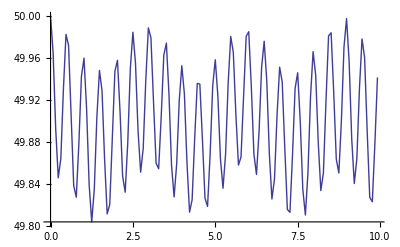

```mathematica
ListPlot[{times,AvgJzS}ᵀ,Joined->True]
```

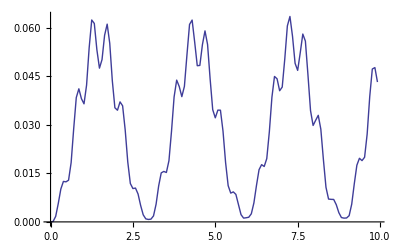

```mathematica
ListPlot[{times,AvgJz2-AvgJzS}ᵀ,Joined->True]
```